# MFEM Mesh Generation

Instructions:
Use mesh tools to create an ElementMesh object for the mesh that you want. 
Set the proper conditions for the BoundaryElement attributes.
For 2D write “2” after numVertices.
Set the proper numbers for element type and boundary element type. 
Set the proper dimension.
Add all the relevant boundaryElement lists.
Export.

```mathematica
<<NDSolve`FEM`
<<MeshTools`
<<Notation`
<< HKLaTeXWrite`
```

```mathematica
Symbolize[Subscript[R, o]];Symbolize[Subscript[R, i]];
```

### Mesh Generation

```mathematica
L=5;W=5;
```

ElementMesh[{{0.,5.},{0.,5.}},{QuadElement[<25>]}]

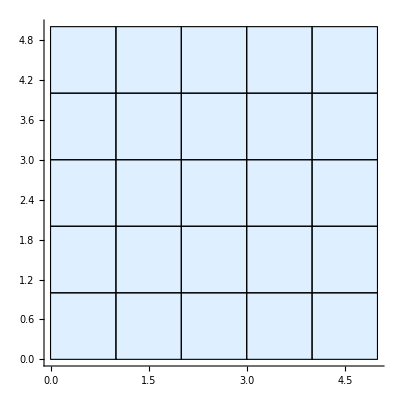

```mathematica
mesh =RectangleMesh[{0,0},{L,W},{5,5}]
Show[mesh["Wireframe"["MeshElementStyle"->FaceForm[LightBlue]]],Axes->True]
```

```mathematica
coords=mesh["Coordinates"]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

25

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

20

```mathematica
boundaryElements
```

{{1,7},{2,1},{3,2},{4,3},{5,4},{12,6},{6,5},{7,13},{18,12},{13,19},{24,18},{19,25},{30,24},{25,31},{31,32},{32,33},{33,34},{34,35},{35,36},{36,30}}

```mathematica
(* Assign boundary attributes *)
```

```mathematica
(* boundary at Subscript[X, _]=0 *)
boundaryElements1 := Module[{elcoords,belements1,zcoords,count},
belements1 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]]<= 0.00001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements1,i]
 ];
,{i,boundaryElements}];
belements1
]
```

```mathematica
(* boundary at Subscript[X, _]=L *)
boundaryElements2 := Module[{elcoords,belements2,zcoords,count},
belements2 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]]<= 0.0001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements2,i]
 ];
,{i,boundaryElements}];
belements2
]
```

```mathematica
(* Inner surface , i.e., Sqrt[Subscript[X, 1]^2+Subscript[X, 2]^2] <= (Subscript[R, i]+0.00001) *)
boundaryElements3 := Module[{elcoords,belements3,zcoords,count},
belements3 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,1]] >= (L-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements3,i]
 ];
,{i,boundaryElements}];
belements3
]
```

```mathematica
(* Inner surface , i.e., Sqrt[Subscript[X, 1]^2+Subscript[X, 2]^2] <= (Subscript[R, i]+0.00001) *)
boundaryElements4 := Module[{elcoords,belements3,zcoords,count},
belements3 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,2]] >= (W-0.0001), count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==2, AppendTo[belements3,i]
 ];
,{i,boundaryElements}];
belements3
]
```

```mathematica
boundaryElements//Length
boundaryElements1//Length
boundaryElements2//Length
boundaryElements3//Length
boundaryElements4//Length
```

20

5

5

5

«1 more identical outputs»

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[2],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]],"\n"],{x,coords}]]];
(* *)
```

```mathematica
(*Build elements section*)
elementSection=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 3 ",(*1=region attr,3=square, 4=tetrahedron, 5=cuboid*)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 1 ",(*1=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 1 ",(*2=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 1 ",(*3=boundary attr, 1=line segment, 2=triangle, 3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
boundarySection4=StringJoin[
StringJoin[Table[StringJoin["4 1 ",(*1=boundary attr, 1=line segment, 2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements4}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"2"<>"\n\n",elementSection,"\n",boundarySection1,boundarySection2,boundarySection3,boundarySection4,"\n",vertexSection]; (* Set the dimension appropriately *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/Projects/MeshFiles

```mathematica
Export["Rectangle-quad.mesh",mfemMeshContent,"Text"]
```

Rectangle-quad.mesh